```mathematica
a=0.1;b=0.05;f1[k_]:=Sqrt[a^2+b^2+Sqrt[2 a^2 b^2 (1+Cos[2 k])]];f2[k_]:=Sqrt[a^2+b^2-Sqrt[2 a^2 b^2 (1+Cos[2 k])]];f3[k_]:=Sqrt[a^2+b^2+2 a b Cos[k]];
```

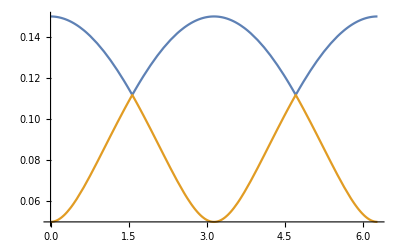

```mathematica
Plot[{f1[k],f2[k]},{k,0,2Pi}]
```

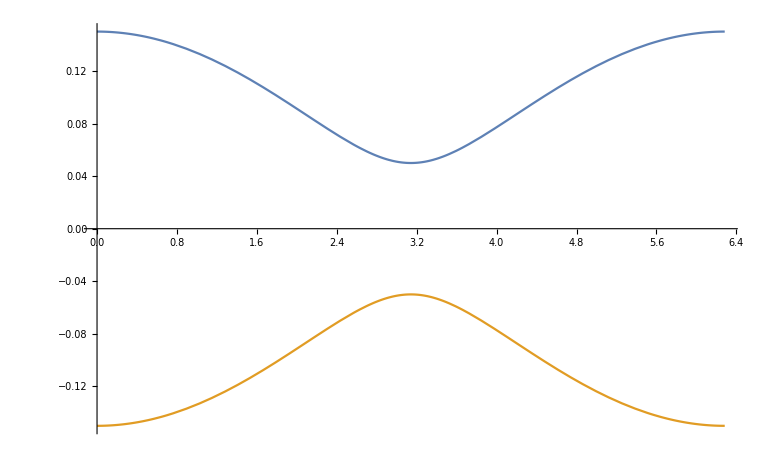

```mathematica
Plot[{f3[k],-f3[k]},{k,0,2Pi}]
```

```mathematica
Clear[b]
```

```mathematica
Integrate[Sqrt[a^2+b^2+2 a b Cos[k]],k]
```

(2 √(a^2+b^2+2 a b Cos[k]) EllipticE[k/2,(4 a b)/(a+b)^2])/(√((a^2+b^2+2 a b Cos[k])/(a+b)^2))

```mathematica
f[k_]:=(2 √(a^2+b^2+2 a b Cos[k]) EllipticE[k/2,(4 a b)/(a+b)^2])/(√((a^2+b^2+2 a b Cos[k])/(a+b)^2));
```

```mathematica
f[2 Pi]
```

(4 √(a^2+2 a b+b^2) EllipticE[(4 a b)/(a+b)^2])/(√((a^2+2 a b+b^2)/(a+b)^2))

```mathematica
FullSimplify[f[2 Pi]-f[0]]
```

4 √((a+b)^2) EllipticE[(4 a b)/(a+b)^2]

```mathematica
a=-0.7;b=0.69;
```

```mathematica
bt[lambda_]:=b (1+2(1+a)lambda);rho[t_]:=1-2(1+a)t;
```

```mathematica
En[t_,lambda_]:=-1/Pi Sqrt[(bt[lambda] +rho[t])^2] EllipticE[4 bt[lambda]rho[t]/(bt[lambda] +rho[t])^2]-(1+a)t^2+b(1+a)lambda^2;
```

```mathematica
sol=FindRoot[{FullSimplify[D[En[t,lambda],t]]==0,FullSimplify[D[En[t,lambda],lambda]]==0},{{t,0.5},{lambda,0.5}}]
```

{t→0.307079,lambda→0.329475}

```mathematica
t0=Last[First[sol]]
```

0.307079

```mathematica
lambda0=Last[Last[sol]]
```

0.329475

```mathematica
disp[k_]:=Sqrt[(1-2(1+a)t0)^2+(b (1+2(1+a)lambda0))^2+2 (1-2(1+a)t0) (b (1+2(1+a)lambda0)) Cos[k]];
```

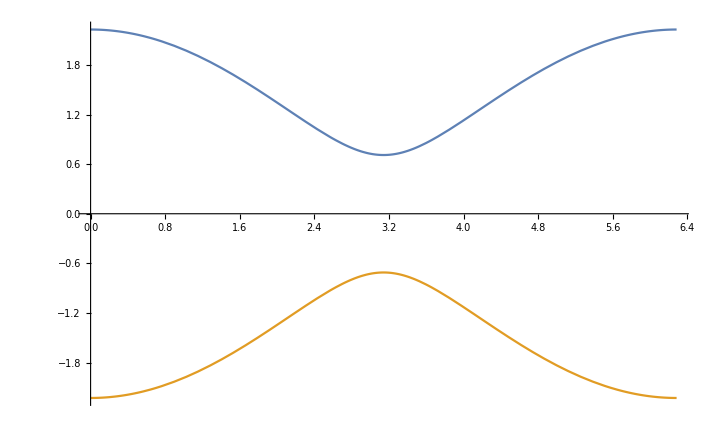

```mathematica
Plot[{disp[k],-disp[k]},{k,0,2Pi}]
```

```mathematica
gap=2 disp[Pi]
```

0.0212998

```mathematica
Clear[gap]
```

```mathematica
amin=-0.99;amax=-0.01;bmin=0.01;bmax=1.0;ngrid=10;For[i=0,i≤ngrid,i++,For[j=0,j≤ngrid,j++,a=amin+i/ngrid*(amax-amin);b=bmin+j/ngrid*(bmax-bmin);bt[lambda_]:=b (1+2(1+a)lambda);rho[t_]:=1-2(1+a)t;En[t_,lambda_]:=-1/Pi Sqrt[(bt[lambda] +rho[t])^2] EllipticE[4 bt[lambda]rho[t]/(bt[lambda] +rho[t])^2]-(1+a)t^2+b(1+a)lambda^2;sol=FindRoot[{FullSimplify[D[En[t,lambda],t]]==0,FullSimplify[D[En[t,lambda],lambda]]==0},{{t,0.5},{lambda,0.5}}];t0=Last[First[sol]];lambda0=Last[Last[sol]];
(*dont really get the disp[k_] part*)
disp[k_]:=Sqrt[(1-2(1+a)t0)^2+(b (1+2(1+a)lambda0))^2+2 (1-2(1+a)t0) (b (1+2(1+a)lambda0)) Cos[k]];gap[i][j]=2 disp[Pi]]];
```

```mathematica
ListDensityPlot[Flatten[Table[{amin+i/ngrid*(amax-amin),bmin+j/ngrid*(bmax-bmin),gap[i][j]},{i,0,ngrid},{j,0,ngrid}],1]]
```

-Graphics-

```mathematica
Dimensions[Table[{amin+i/ngrid*(amax-amin),bmin+j/ngrid*(bmax-bmin),gap[i][j]},{i,0,ngrid},{j,0,ngrid}]]
```

{11,11,3}

```mathematica
Dimensions[Flatten[Table[{amin+i/ngrid*(amax-amin),bmin+j/ngrid*(bmax-bmin),gap[i][j]},{i,0,ngrid},{j,0,ngrid}],1]]
```

{121,3}

```mathematica
Flatten[Table[{amin+i/ngrid*(amax-amin),bmin+j/ngrid*(bmax-bmin),gap[i][j]},{i,0,ngrid},{j,0,ngrid}],1]
```

{{-0.99,0.01,1.96},{-0.99,0.109,1.76194},{-0.99,0.208,1.56378},{-0.99,0.307,1.36553},{-0.99,0.406,1.16717},{-0.99,0.505,0.968703},{-0.99,0.604,0.77013},{-0.99,0.703,0.571441},{-0.99,0.802,0.372627},{-0.99,0.901,0.173671},{-0.99,1.,0.0254622},{-0.892,0.01,1.76399},{-0.892,0.109,1.56537},{-0.892,0.208,1.3657},{-0.892,0.307,1.16498},{-0.892,0.406,0.963198},{-0.892,0.505,0.760326},{-0.892,0.604,0.556332},{-0.892,0.703,0.351177},{-0.892,0.802,0.144852},{-0.892,0.901,0.0622645},{-0.892,1.,0.273398},{-0.794,0.01,1.56799},{-0.794,0.109,1.36887},{-0.794,0.208,1.16791},{-0.794,0.307,0.965147},{-0.794,0.406,0.760595},{-0.794,0.505,0.554278},{-0.794,0.604,0.346263},{-0.794,0.703,0.136886},{-0.794,0.802,0.0718189},{-0.794,0.901,0.291303},{-0.794,1.,0.516462},{-0.696,0.01,1.37199},{-0.696,0.109,1.17259},{-0.696,0.208,0.971028},{-0.696,0.307,0.767487},{-0.696,0.406,0.56213},{-0.696,0.505,0.355192},{-0.696,0.604,0.147435},{-0.696,0.703,0.0561575},{-0.696,0.802,0.279228},{-0.696,0.901,0.513668},{-0.696,1.,0.754},{-0.598,0.01,1.17599},{-0.598,0.109,0.97688},{-0.598,0.208,0.776459},{-0.598,0.307,0.575229},{-0.598,0.406,0.37348},{-0.598,0.505,0.171944},{-0.598,0.604,0.0212962},{-0.598,0.703,0.239819},{-0.598,0.802,0.479859},{-0.598,0.901,0.730029},{-0.598,1.,0.986414},{-0.5,0.01,0.98},{-0.5,0.109,0.782587},{-0.5,0.208,0.587457},{-0.5,0.307,0.394888},{-0.5,0.406,0.20431},{-0.5,0.505,0.0196686},{-0.5,0.604,0.178026},{-0.5,0.703,0.417886},{-0.5,0.802,0.674645},{-0.5,0.901,0.941273},{-0.5,1.,1.21437},{-0.402,0.01,0.784038},{-0.402,0.109,0.591978},{-0.402,0.208,0.411128},{-0.402,0.307,0.236936},{-0.402,0.406,0.0665503},{-0.402,0.505,0.102342},{-0.402,0.604,0.33238},{-0.402,0.703,0.590721},{-0.402,0.802,0.864583},{-0.402,0.901,1.14823},{-0.402,1.,1.43852},{-0.304,0.01,0.588153},{-0.304,0.109,0.411364},{-0.304,0.208,0.259656},{-0.304,0.307,0.111664},{-0.304,0.406,0.0277009},{-0.304,0.505,0.230758},{-0.304,0.604,0.482649},{-0.304,0.703,0.759168},{-0.304,0.802,1.05051},{-0.304,0.901,1.35159},{-0.304,1.,1.65945},{-0.206,0.01,0.392576},{-0.206,0.109,0.256146},{-0.206,0.208,0.14416},{-0.206,0.307,0.0231103},{-0.206,0.406,0.125096},{-0.206,0.505,0.357249},{-0.206,0.604,0.629226},{-0.206,0.703,0.923969},{-0.206,0.802,1.23309},{-0.206,0.901,1.55193},{-0.206,1.,1.87767},{-0.108,0.01,0.199165},{-0.108,0.109,0.14558},{-0.108,0.208,0.0644632},{-0.108,0.307,0.0350318},{-0.108,0.406,0.22537},{-0.108,0.505,0.481163},{-0.108,0.604,0.772642},{-0.108,0.703,1.08573},{-0.108,0.802,1.41288},{-0.108,0.901,1.74974},{-0.108,1.,2.09356},{-0.01,0.01,0.0490003},{-0.01,0.109,0.0780977},{-0.01,0.208,0.013025},{-0.01,0.307,0.104313},{-0.01,0.406,0.32505},{-0.01,0.505,0.602623},{-0.01,0.604,0.913376},{-0.01,0.703,1.24492},{-0.01,0.802,1.59031},{-0.01,0.901,1.94538},{-0.01,1.,2.30747}}

```mathematica
ListPlot3D[Flatten[Table[{amin+i/ngrid*(amax-amin),bmin+j/ngrid*(bmax-bmin),gap[i][j]},{i,0,ngrid},{j,0,ngrid}],1]]
```

-Graphics3D-

-Graphics3D-

```mathematica
a=-0.1;b=0.8;
```

```mathematica
bt[lambda_]:=b (1+2(1+a)lambda);rho[t_]:=1-2(1+a)t;En[t_,lambda_]:=-1/Pi Sqrt[(bt[lambda] +rho[t])^2] EllipticE[4 bt[lambda]rho[t]/(bt[lambda] +rho[t])^2]-(1+a)t^2+b(1+a)lambda^2;sol=FindRoot[{FullSimplify[D[En[t,lambda],t]]==0,FullSimplify[D[En[t,lambda],lambda]]==0},{{t,0.5},{lambda,0.5}}];t0=Last[First[sol]];lambda0=Last[Last[sol]];
```

```mathematica
t0
```

0.13394

```mathematica
lambda0
```

0.464764

```mathematica
Plot3D[En[t,lambda],{t,-0.8,0.8},{lambda,-0.8,0.8}]
```

-Graphics3D-